```mathematica
SetDirectory[NotebookDirectory[]];
data  ={7};
fPrior[λ_]:=PDF[LogNormalDistribution[1,1],λ]
data={7};
fLikelihood[λ_,lData__]:=Likelihood[PoissonDistribution[λ],lData]
aDenominator=NIntegrate[fLikelihood[λ,data]fPrior[λ],{λ,0,∞}];
fPosterior[λ_,lData_,aDenominator_]:=fLikelihood[λ,lData] fPrior[λ]/aDenominator
```

```mathematica
fMCIntegralEstimator[n_,lData_]:=Module[{lSample = RandomVariate[LogNormalDistribution[1,1],{n}],lSampleLikelihood},lSampleLikelihood = fLikelihood[#,lData]&/@lSample; Mean[lSampleLikelihood]]
```

```mathematica
lMeanLikelihood10=ParallelTable[fMCIntegralEstimator[10,data],{10000}];
```

```mathematica
lMeanLikelihood100=ParallelTable[fMCIntegralEstimator[100,data],{10000}];
```

```mathematica
lMeanLikelihood1000=ParallelTable[fMCIntegralEstimator[1000,data],{10000}];
```

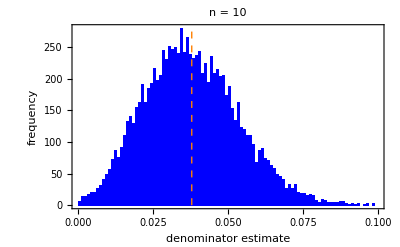

```mathematica
g1=Histogram[lMeanLikelihood10,100,ChartStyle->Blue,PlotRange->{{0,0.1},Full},Epilog->{Thick,Dashed,Orange,Line[{{aDenominator,0},{aDenominator,10000}}]},Frame->{True,True,False,False},Axes->{True,False},FrameLabel->{"denominator estimate","frequency"},BaseStyle->{FontSize->14},PlotLabel->"n = 10"]
```

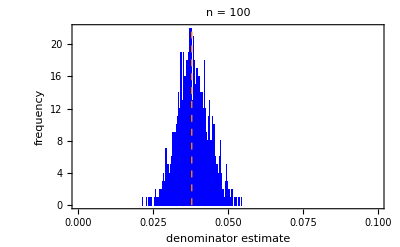

```mathematica
g2=Histogram[lMeanLikelihood100,100,ChartStyle->Blue,PlotRange->{{0,0.1},Full},Epilog->{Thick,Dashed,Orange,Line[{{aDenominator,0},{aDenominator,10000}}]},Frame->{True,True,False,False},Axes->{True,False},FrameLabel->{"denominator estimate","frequency"},BaseStyle->{FontSize->14},PlotLabel->"n = 100"]
```